```mathematica
V[T_,i_]:=1.256-2.26*10^-4*T-2*8.3145*T/96485*ArcSinh[(i+0.001)/(2*8*10^-5)]-i*0.05+0.12*Log[1-i/0.7]
P[w_,i_, T_]:=3+10^-3*4650*w^2/(60*125*3)-150*i*V[T,i]*3
```

```mathematica
4*0.18*P[800,0,400]/24
```

4.058

```mathematica
P[100,0,0]
```

5.06667

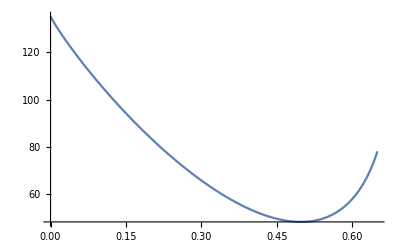

```mathematica
Plot[P[100,i,400],{i,0,0.65}]
```

```mathematica
Plot3D[P[w, i, 273],{i,0,0.65},{w,0,100}]
```

-Graphics3D-

```mathematica
Maximize[{P[w,i,273], 0≤ w≤ 100,  0 ≤ i ≤ 0.65},{w,i}]
```

{5.06667,{w→100.,i→6.87172×10^-12}}

```mathematica
Minimize[{P[w,i,400], 0≤ w≤ 100,  0 ≤ i ≤ 0.65},{w,i}]
```

{-84.2082,{w→0.00610825,i→0.497864}}

```mathematica
Solve[4*0.18*p/24==9, p ,Reals]
```

{{p→300.}}